## 函数定义

```mathematica
(*使用前先运行这个*)
(*------------------------*)
(*SimTrans 依据给定的不动点和变换矩阵生成对应的仿射变换*)
SimTrans[s_,fp_]:=Module[{mat},
mat=If[MatrixQ[s],s,ScalingMatrix[Table[s,Length[fp]]]];
AffineTransform[{mat,fp-mat.fp}]];
(*ConvertFun 用于内部转换人工输入的函数*)
ConvertFun[f_]:=Module[{g},
g=f;
If[!ValueQ[f["ArgumentLength"]],
g["AffineQ"]=False;
g["Self"]=False;
Which[(*计算维数*)
ValueQ[f[{0,0}]],g["ArgumentLength"]=2,
ValueQ[f[{0}]],g["ArgumentLength"]=1,
ValueQ[f[{0,0,0}]],g["ArgumentLength"]=3
]];
If[!ValueQ[g["ArgumentLength"]],
g["ArgumentLength"]=-1];
g
];
(*FixPoint 计算不动点，如果是仿射变换返回的是精确值，否则是迭代后的值*)
FixPoint[f_]:=
If[f["AffineQ"],
Inverse[IdentityMatrix[f["ArgumentLength"]]-f["AffineMatrix"]].f["AffineVector"],
Nest[f,Table[1.0,f["ArgumentLength"]],10]
];
Options[DrawFrac]={Method->Automatic,MaxIterations->Automatic,Axes->False,"Approximation"->True,"Size"->0.02};
(*DrawFrac 根据函数序列绘制图像，可选一些方法选项*)
DrawFrac[f_,opts:OptionsPattern[]]:=(*sf:List of Transformation;t:iteration count,default to make 10000 points*)
Module[{sf,ls,l,c,ti,md,pr,ax,ap,sst,afq,line,sz},
ti=OptionValue[MaxIterations];
md=OptionValue[Method];
ax=OptionValue[Axes];
ap=OptionValue["Approximation"];
sz=OptionValue["Size"];
sf=ConvertFun/@f;
afq=AllTrue[sf,!(ValueQ[#["Self"]])&];
If[!afq&&md=="ConvexHull",Message[DrawFrac::ch];Abort[]];
ls=Through[sf["ArgumentLength"]];
(*find if dimensions are same*)
If[!AllTrue[ls,SameQ[First[ls],#]&],Message[DrawFrac::wd,ls];Abort[]];
l=ls[[1]];(*dimension*)
c=Length[sf];
If[ti==Automatic,ti=If[l==1,Floor[Log[c,100]],Floor[Log[c,10000]]]];
(*choose method*)
If[md==Automatic,md=Switch[l,1,"Points",2,"Points",
3,If[afq,"ConvexHull","Points"]]];
If[!MemberQ[{"Points","ConvexHull","Lines"},md],Message[DrawFrac::md];Abort[]];
Switch[md,
"Points",
If[ap,sst=N[Through[sf[#]]]&,sst=Through[sf[#]]&];
Switch[l,
1,
NumberLinePlot[Flatten[#],PlotStyle->{PointSize[Small],Opacity[1]},Axes->ax]&/@NestList[Flatten[Map[sst,#1],1]&,{{0}},ti](*//GraphicsColumn*),
2,
(*ListPlot[#,PlotStyle->{PointSize[Small],Opacity[1]},Axes->False,PlotRange->{{-1,1},{-1,1}},AspectRatio->1,ImagePadding->None]*)MapThread[Graphics[{PointSize[#1],Gray,Point[#2]},Axes->ax]&,{Table[sz*0.85^n,{n,0,ti}],NestList[Flatten[Map[sst,#1],1]&,{{0,0}},ti]}],
3,
MapThread[Graphics3D[{PointSize[#1],Gray,Point[#2]},Axes->ax]&,{Table[sz*0.85^n,{n,0,ti}],NestList[Flatten[Map[sst,#1],1]&,{{0,0,0}},ti]}],
_,Message[DrawFrac::wd,ls];Abort[]
],
"Lines",
If[ap,
sst[lines_]:=Flatten[ReplaceAll[Line[pts_]:>Line[#/@pts]][lines]&/@sf],
sst[lines_]:=Flatten[ReplaceAll[Line[pts_]:>Line[#/@pts]][lines]&/@sf]
];
Switch[l,
1,
Graphics[{AbsolutePointSize[0],EdgeForm[],#},Axes->ax,AspectRatio->1/4]&/@NestList[RegionUnion[Through[sf[#]]]&,ConvexHullMesh[FixPoint/@sf](*Cube[]*),ti],
2,
line=MeshPrimitives[ConvexHullMesh[FixPoint/@sf],1];
Graphics[{AbsoluteThickness[sz],#},Axes->ax]&/@NestList[sst,line,ti]
,
3,
line=MeshPrimitives[ConvexHullMesh[FixPoint/@sf],1];
Graphics3D[{AbsoluteThickness[sz],#},Axes->ax,Boxed->ax]&/@NestList[sst,line,ti],
_,Message[DrawFrac::wd,ls];Abort[]
],
"ConvexHull",
If[ap,sst=N[FixPoint[#]]&,sst=FixPoint];
Switch[l,
1,
Graphics[{AbsolutePointSize[0],EdgeForm[],#},Axes->ax,AspectRatio->1/4]&/@NestList[RegionUnion[Through[sf[#]]]&,ConvexHullMesh[sst/@sf](*Cube[]*),ti],
2,
Graphics[{EdgeForm[],#},Axes->ax]&/@NestList[RegionUnion[Through[sf[#]]]&,ConvexHullMesh[sst/@sf](*Cube[]*),ti],
3,
Graphics3D[{EdgeForm[],#},Axes->ax,Boxed->ax]&/@NestList[RegionUnion[Through[sf[#]]]&,ConvexHullMesh[sst/@sf](*Cube[]*),ti],
_,Message[DrawFrac::wd,ls];Abort[]
]
]
]
DrawFrac::md="Method:Points,ConvexHull,Lines";
DrawFrac::ch="Method ConvexHull does not apply to non affine transformation";
DrawFrac::wd="Dimension `1` should be same and less than 3";
```

## 说明

### 变换函数

AffineTransform是自带的函数，输入是给定矩阵和平移向量

```mathematica
AffineTransform[{{{Subscript[a, 1,1],Subscript[a, 1,2]},{Subscript[a, 2,1],Subscript[a, 2,2]}},{Subscript[b, 1],Subscript[b, 2]}}]
```

TransformationFunction[(a_(1,1) | a_(1,2) | b_1
a_(2,1) | a_(2,2) | b_2
0 | 0 | 1)]

常见的矩阵函数有单位、缩放、旋转矩阵

```mathematica
IdentityMatrix[2]//MatrixForm
```

(1 | 0
0 | 1)

```mathematica
ScalingMatrix[{1/3,1/2,-1/2}]//MatrixForm
```

(1/3 | 0 | 0
0 | 1/2 | 0
0 | 0 | -1/2)

```mathematica
RotationMatrix[Pi/3]//MatrixForm
```

(1/2 | -(√3)/2
(√3)/2 | 1/2)

```mathematica
EulerMatrix[{Pi/2,Pi/3,-Pi/6}]//MatrixForm
```

(1/2 | -(√3)/2 | 0
(√3)/4 | 1/4 | (√3)/2
-3/4 | -(√3)/4 | 1/2)

仅在本文档中有SimTrans函数，用于已知不动点和矩阵计算相似变换，它支持两种输入方式

```mathematica
SimTrans[1/2,{0,0,1}](*统一缩放率的输入，格式是SimTrans[缩放率，不动点]*)
```

TransformationFunction[(1/2 | 0 | 0 | 0
0 | 1/2 | 0 | 0
0 | 0 | 1/2 | 1/2
0 | 0 | 0 | 1)]

```mathematica
SimTrans[RotationMatrix[Pi/6].ScalingMatrix[{1/3,1/2}],{-1,1}](*用矩阵作为输入，格式是SimTrans[矩阵，不动点]*)
```

TransformationFunction[(1/(2 √3) | -1/4 | 1/12 (-9+2 √3)
1/6 | (√3)/4 | 1/12 (14-3 √3)
0 | 0 | 1)]

TransformationFunction也可以表示分式线性变换，由 r 映射到 (A.r+b)/(c.r+d).

```mathematica
LinearFractionalTransform[{{{1,2},{3,4}}, {5,6},{7,8}}]
```

TransformationFunction[(1 | 2 | 5
3 | 4 | 6
7 | 8 | 1)]

### 绘图

主要的输入是由TransformationFunction构成的序列 ，支持其他多元函数

```mathematica
(*Cantor Set*)
can={AffineTransform[{ScalingMatrix[{1/3}],{0}}],
AffineTransform[{ScalingMatrix[{1/3}],{2/3}}]}
```

{TransformationFunction[(1/3 | 0
0 | 1)],TransformationFunction[(1/3 | 2/3
0 | 1)]}

```mathematica
pt=DrawFrac[can]
```

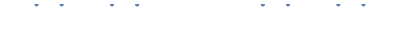
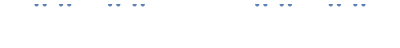
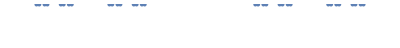
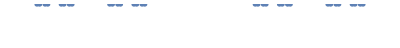
```mathematica
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

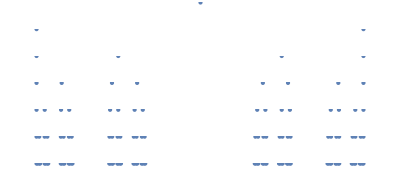

```mathematica
pt//GraphicsColumn
```

使用Method选项控制绘图方法，可选方法有“Points”,“Lines”,“ConvexHull”，表示画点、线、或者凸包区域
默认方法是一维、二维画点，三维使用凸包区域
自建函数的区域绘制较为困难，现在不支持使用自建函数的凸包方法

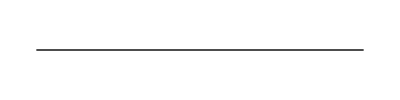
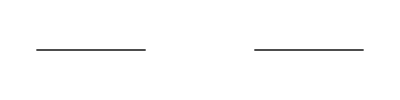
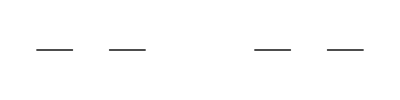
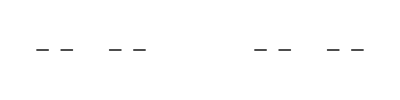
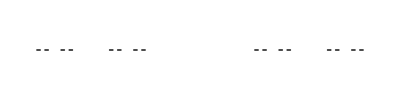
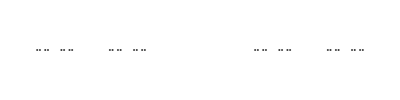
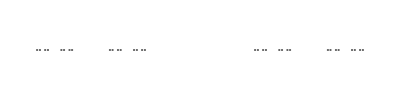

```mathematica
DrawFrac[can,Method->"ConvexHull"]
```

```mathematica
(*Sierpinski Triangle*)
strig={AffineTransform[{ScalingMatrix[{1/2,1/2}],{0,1/2}}],AffineTransform[{ScalingMatrix[{1/2,1/2}],{Sqrt[3]/6,0}}],AffineTransform[{ScalingMatrix[{1/2,1/2}],{-Sqrt[3]/6,0}}]}
```

{TransformationFunction[(1/2 | 0 | 0
0 | 1/2 | 1/2
0 | 0 | 1)],TransformationFunction[(1/2 | 0 | 1/(2 √3)
0 | 1/2 | 0
0 | 0 | 1)],TransformationFunction[(1/2 | 0 | -1/(2 √3)
0 | 1/2 | 0
0 | 0 | 1)]}

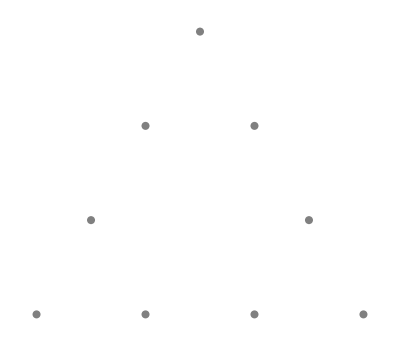
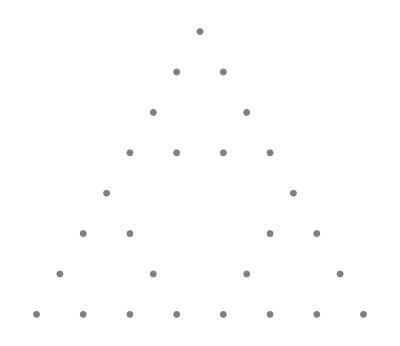
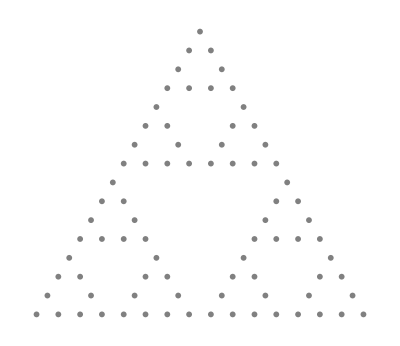
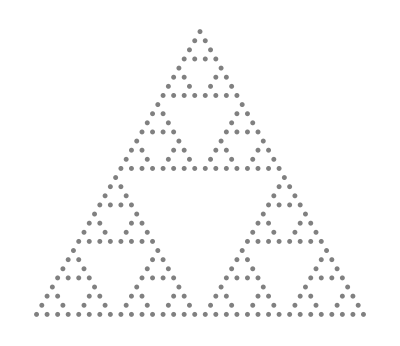
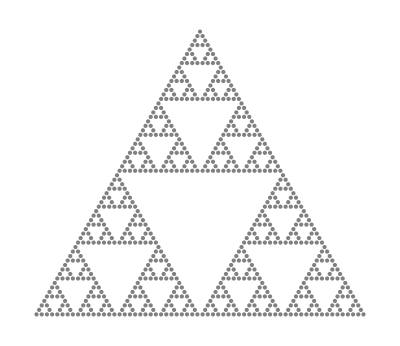
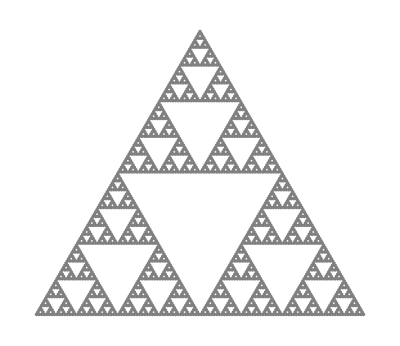
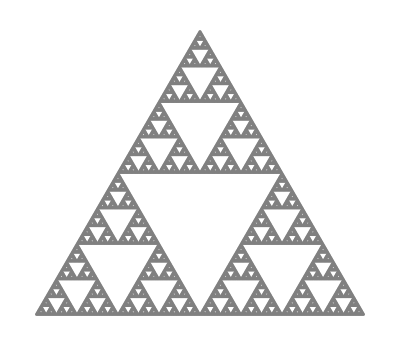
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
DrawFrac[strig]
```

如果想使用线性变换以外的函数，按照如下格式：f[{x_,y_}]:={f_1(x,y),f_2(x,y)}，这个格式会在画图函数内部处理匹配适合的方法

```mathematica
ff[{x_,y_}]:={x/2+Sin[x]/10,y/2+1/2};
mstrig={ff,AffineTransform[{ScalingMatrix[{1/2,1/2}],{Sqrt[3]/6,0}}],AffineTransform[{ScalingMatrix[{1/2,1/2}],{-Sqrt[3]/6,0}}]}
```

{ff,TransformationFunction[(1/2 | 0 | 1/(2 √3)
0 | 1/2 | 0
0 | 0 | 1)],TransformationFunction[(1/2 | 0 | -1/(2 √3)
0 | 1/2 | 0
0 | 0 | 1)]}

使用MaxIterations选项控制迭代次数，默认画10000个点

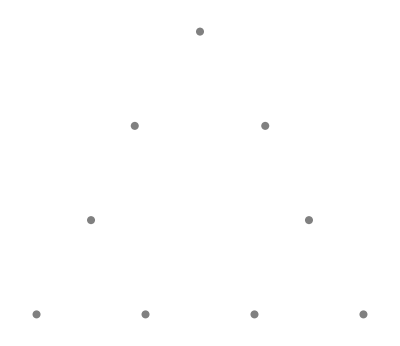
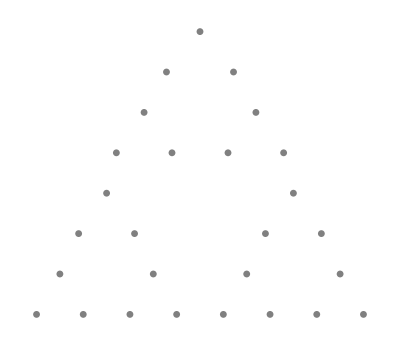
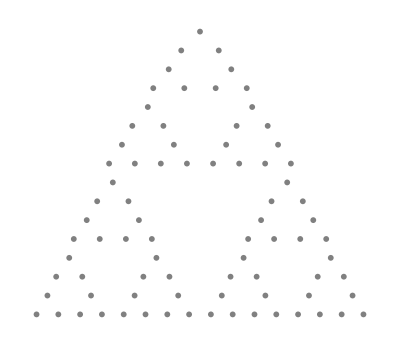
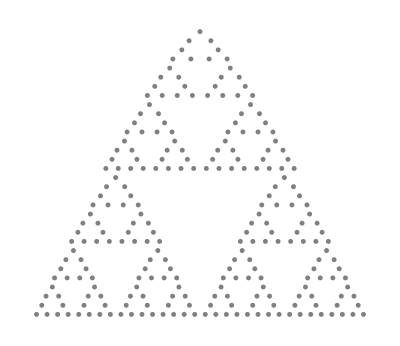
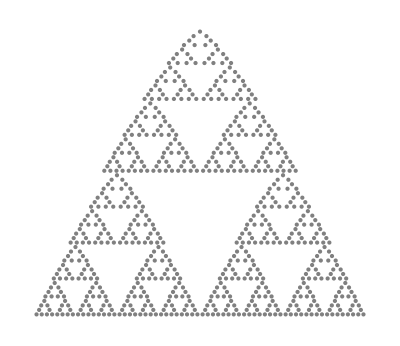
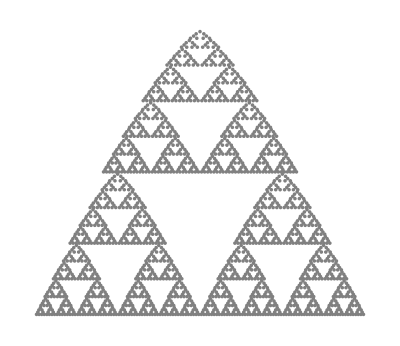
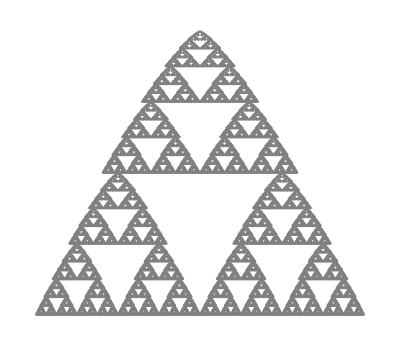
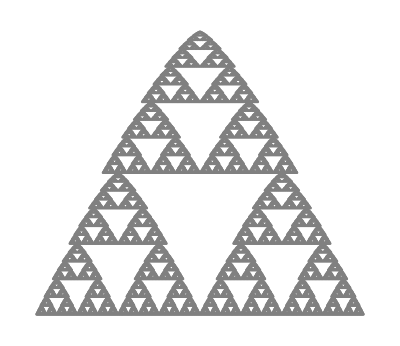
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
DrawFrac[mstrig,Method->"Points",MaxIterations->9]
```

其他的例子

```mathematica
vcurve={AffineTransform[{ScalingMatrix[{1/3,1/3}],{0,0}}],AffineTransform[{RotationMatrix[Pi/3].ScalingMatrix[{1/3,1/3}],{1/3,0}}],AffineTransform[{RotationMatrix[-Pi/3].ScalingMatrix[{1/3,1/3}],{1/2,Sqrt[3]/6}}],AffineTransform[{ScalingMatrix[{1/3,1/3}],{2/3,0}}]};
```

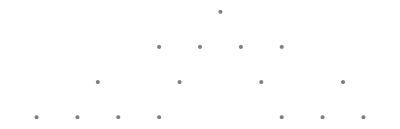
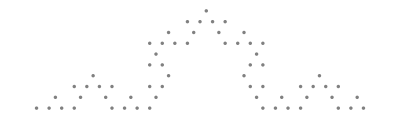
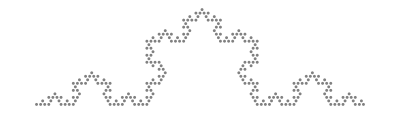
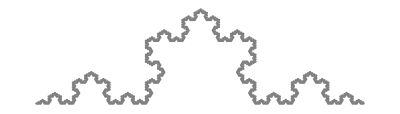
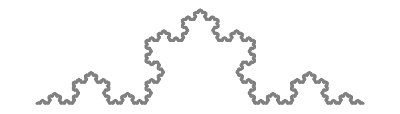
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
DrawFrac[vcurve]
```

```mathematica
scarpet={AffineTransform[{ScalingMatrix[{1/3,1/3}],{0,0}}],AffineTransform[{ScalingMatrix[{1/3,1/3}],{0,1/3}}],AffineTransform[{ScalingMatrix[{1/3,1/3}],{0,2/3}}],AffineTransform[{ScalingMatrix[{1/3,1/3}],{1/3,0}}],AffineTransform[{ScalingMatrix[{1/3,1/3}],{1/3,2/3}}],AffineTransform[{ScalingMatrix[{1/3,1/3}],{2/3,0}}],AffineTransform[{ScalingMatrix[{1/3,1/3}],{2/3,1/3}}],AffineTransform[{ScalingMatrix[{1/3,1/3}],{2/3,2/3}}]};
```


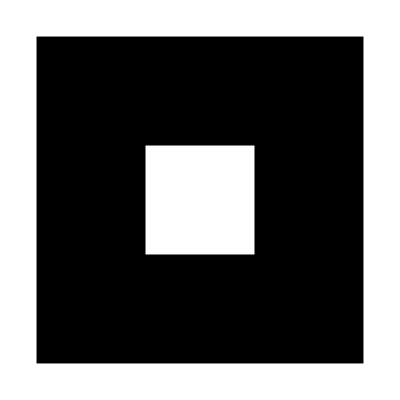
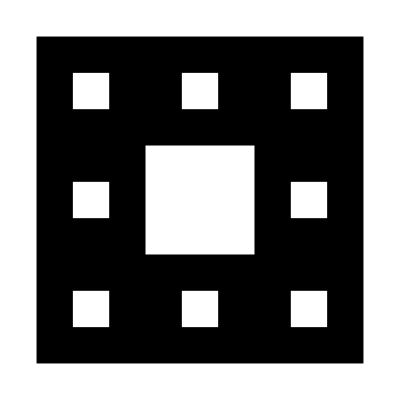
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
DrawFrac[scarpet,Method->"ConvexHull"]
```

```mathematica
cdust={AffineTransform[{ScalingMatrix[{1/4,1/4}],{1/2,3/4}}],AffineTransform[{ScalingMatrix[{1/4,1/4}],{0,1/2}}],AffineTransform[{ScalingMatrix[{1/4,1/4}],{3/4,1/4}}],AffineTransform[{ScalingMatrix[{1/4,1/4}],{1/4,0}}]};
```

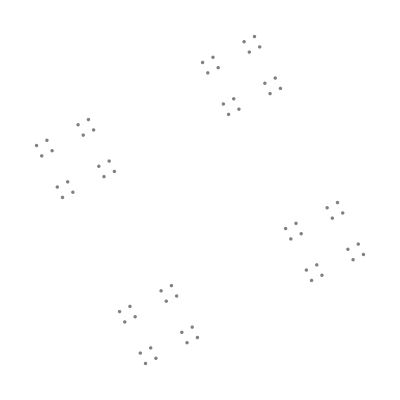
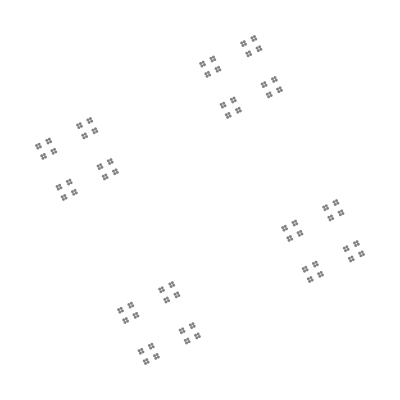
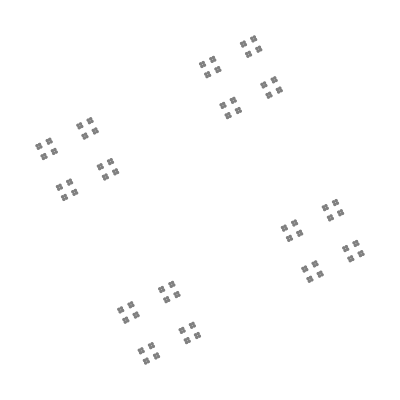
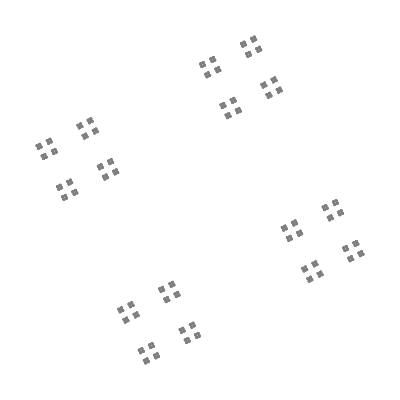
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
DrawFrac[cdust]
```

```mathematica
msp={AffineTransform[{ScalingMatrix[{1/3,1/3,1/3}],{0,0,0}}],AffineTransform[{ScalingMatrix[{1/3,1/3,1/3}],{0,1/3,0}}],AffineTransform[{ScalingMatrix[{1/3,1/3,1/3}],{0,2/3,0}}],AffineTransform[{ScalingMatrix[{1/3,1/3,1/3}],{1/3,0,0}}],AffineTransform[{ScalingMatrix[{1/3,1/3,1/3}],{1/3,2/3,0}}],AffineTransform[{ScalingMatrix[{1/3,1/3,1/3}],{2/3,0,0}}],AffineTransform[{ScalingMatrix[{1/3,1/3,1/3}],{2/3,1/3,0}}],AffineTransform[{ScalingMatrix[{1/3,1/3,1/3}],{2/3,2/3,0}}],AffineTransform[{ScalingMatrix[{1/3,1/3,1/3}],{0,0,1/3}}],AffineTransform[{ScalingMatrix[{1/3,1/3,1/3}],{2/3,0,1/3}}],AffineTransform[{ScalingMatrix[{1/3,1/3,1/3}],{0,2/3,1/3}}],AffineTransform[{ScalingMatrix[{1/3,1/3,1/3}],{2/3,2/3,1/3}}],AffineTransform[{ScalingMatrix[{1/3,1/3,1/3}],{0,0,2/3}}],AffineTransform[{ScalingMatrix[{1/3,1/3,1/3}],{0,1/3,2/3}}],AffineTransform[{ScalingMatrix[{1/3,1/3,1/3}],{0,2/3,2/3}}],AffineTransform[{ScalingMatrix[{1/3,1/3,1/3}],{1/3,0,2/3}}],AffineTransform[{ScalingMatrix[{1/3,1/3,1/3}],{1/3,2/3,2/3}}],AffineTransform[{ScalingMatrix[{1/3,1/3,1/3}],{2/3,0,2/3}}],AffineTransform[{ScalingMatrix[{1/3,1/3,1/3}],{2/3,1/3,2/3}}],AffineTransform[{ScalingMatrix[{1/3,1/3,1/3}],{2/3,2/3,2/3}}]};
```

```mathematica
DrawFrac[msp,"Approximation"->True]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
spyramid={SimTrans[1/2,{0,0,Sqrt[6]/3}],
SimTrans[1/2,{0,1/Sqrt[3],0}],
SimTrans[1/2,{1/2,-1/(2Sqrt[3]),0}],
SimTrans[1/2,{-1/2,-1/(2Sqrt[3]),0}]
};
```

使用Axes控制绘制坐标轴

```mathematica
DrawFrac[spyramid,Method->"Lines",MaxIterations->4,Axes->True]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

## 可能的问题

维度需要一致，不能高于三维

```mathematica
str={AffineTransform[{ScalingMatrix[{1/2}],{0}}],
AffineTransform[{ScalingMatrix[{1/2,1/2}],{Sqrt[3]/6,0}}],AffineTransform[{ScalingMatrix[{1/2,1/2}],{-Sqrt[3]/6,0}}]};
```

```mathematica
DrawFrac[str]
```

DrawFrac::wd: Dimension {1,2,2} should be same and less than 3

$Aborted

不支持非TransformationFunction的凸包方法

```mathematica
ff[{x_,y_}]:={x/2+Sin[x]/10,y/2+1/2};
DrawFrac[{ff,AffineTransform[{ScalingMatrix[{1/2,1/2}],{Sqrt[3]/6,0}}],AffineTransform[{ScalingMatrix[{1/2,1/2}],{-Sqrt[3]/6,0}}]},Method->"ConvexHull"]
```

DrawFrac::ch: Method ConvexHull does not apply to non affine transformation

$Aborted

有时会遇到点和凸包不好的情况

```mathematica
astrig={SimTrans[((Sqrt[5]-1)/2)^2,{0,Sqrt[3]/2}],
SimTrans[((Sqrt[5]-1)/2),{-1/2,0}],
SimTrans[((Sqrt[5]-1)/2),{1/2,0}]
};
```

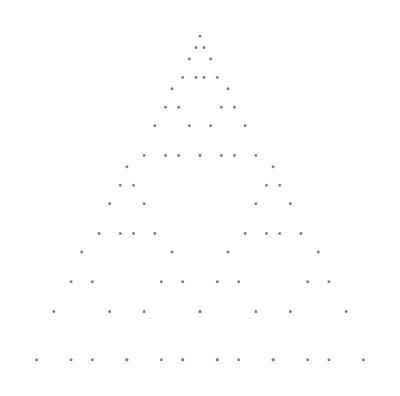
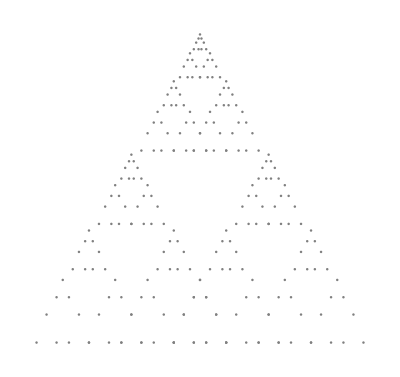
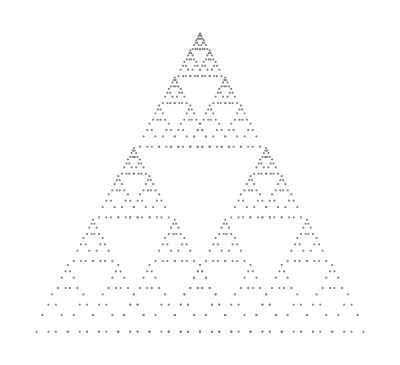
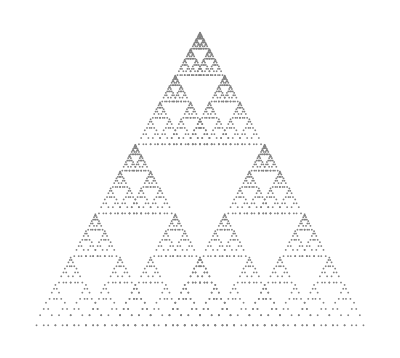
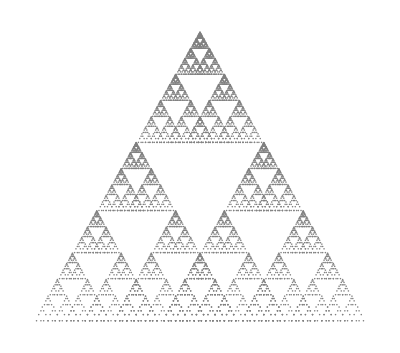
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
DrawFrac[astrig,"Size"->0.01](*使用"Size"控制线的粗细或点的大小*)
```


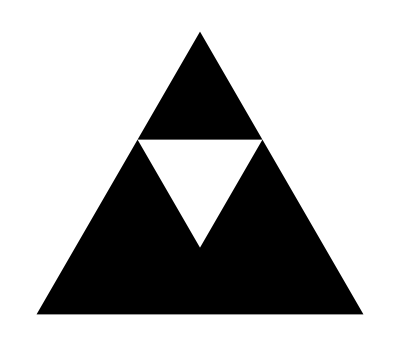
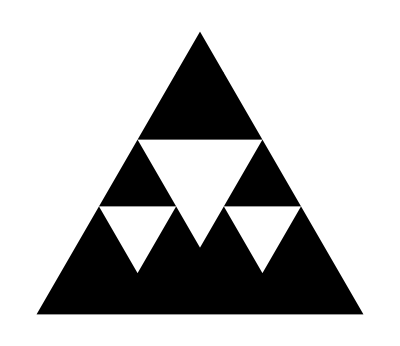
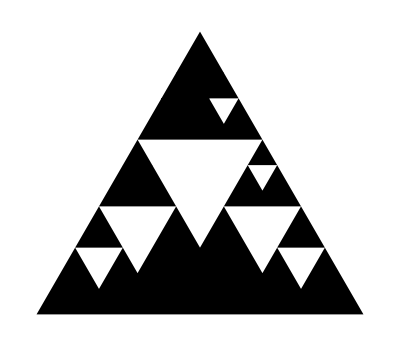
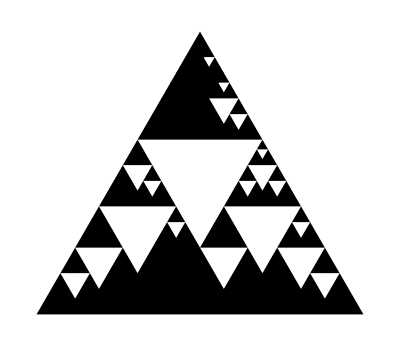
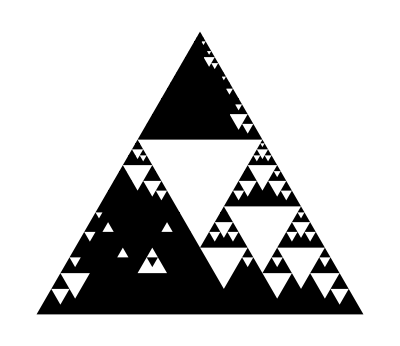

```mathematica
DrawFrac[astrig,Method->"ConvexHull",MaxIterations->5](*可能由于重叠过多渲染失效*)
```

这时使用画线方法相对清楚一些

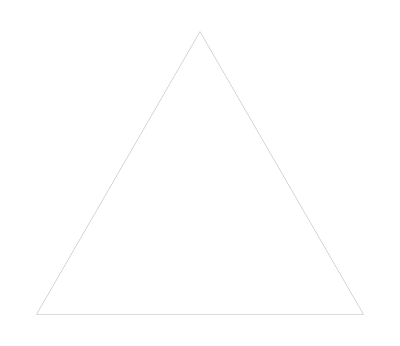
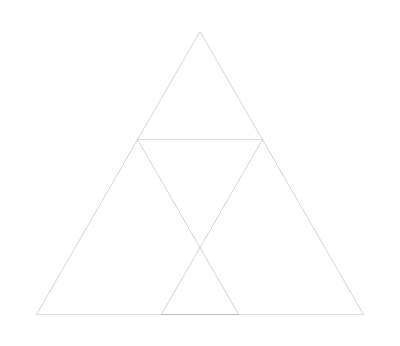
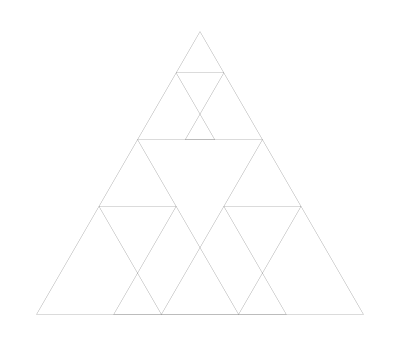
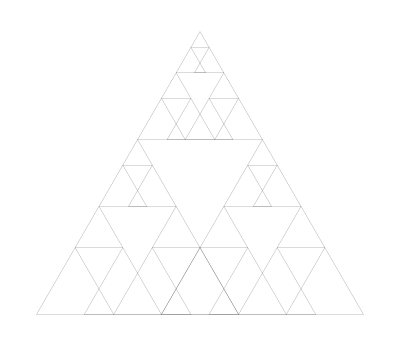
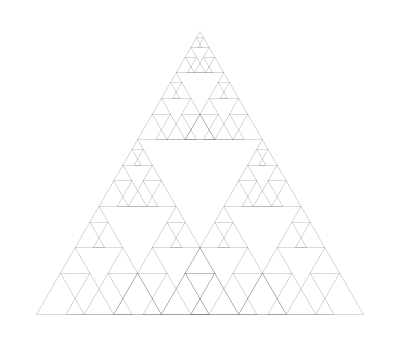
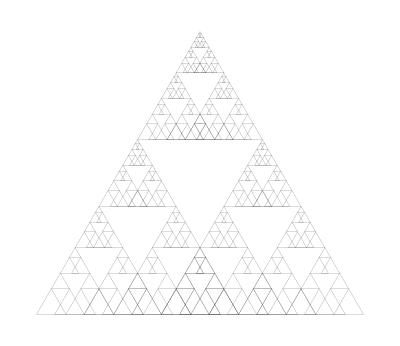
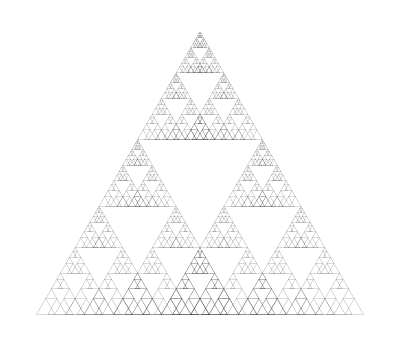
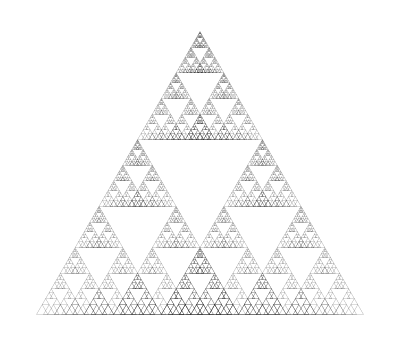

```mathematica
DrawFrac[astrig,Method->"Lines","Size"->0.01]
```